#### Find the closest path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook Variables to change: Tmat, dt, ListSigma

#### choose Tmat

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatRussell;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat=TmatBrownNew;
```

#### check that it’s symmetric, display info

```mathematica
MatrixNote[Tmat]
Tmat==Transpose[Tmat]
PrintVoigt[Tmat]
```

#### Find closest T to ISO

```mathematica
WantDetails="WantDetails";
```

```mathematica
MatrixNote[Tmat]
OutputFor[Tmat,ISO]
```

```mathematica
MatrixNote[Tmat]
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =Closest[Tmat,ISO];  (* ProjToVSigOfU[Tmat,id,ISO]*)
MatrixForm[TISO]
```

#### Matrix norms (not used, but worth thinking about)

```mathematica
MatrixNote[Tmat]
Ntriv =Norm[Tmat,Frobenius]
Niso =Norm[TISO,Frobenius]
Norm[TISO/Niso,Frobenius]
Norm[Ntriv/Ntriv,Frobenius]
```

#### check: the angle does not depend on the size of the T

```mathematica
AngleMatrix[Tmat,TISO]/Degree
AngleMatrix[Tmat/Ntriv,TISO/Niso]/Degree
```

#### Choose Tmat1 and Tmat2

```mathematica
MatrixNote[Tmat]
Tmat1 =TISO;
Tmat2 =Tmat;
```

#### Example: Brown TET triangle TET to XISO segment for the Brown map (set ListSigma={TET,XISO} below) Here TXISO is the closest to TRIV (Pathway 2), and β_XISO = 20.35^o

```mathematica
MatrixNote[Tmat]
OutputFor[Tmat,TET]
TTET=Closest[Tmat,TET];
OutputFor[Tmat,XISO]
TXISO=Closest[Tmat,XISO];
Tmat1=TXISO;
Tmat2=TTET;
MatrixForm[TXISO]
```

#### Example: Brown TET parabola TET to CUBE segment for the Brown map (set ListSigma={TET,CUBE} below) Here TCUBE is the closest to TRIV (Pathway 2), and β_CUBE = 24.34^o

```mathematica
(* MatrixNote[Tmat]
OutputFor[Tmat,TET]
TTET=Closest[Tmat,TET];
OutputFor[Tmat,CUBE]
TCUBE=Closest[Tmat,CUBE];
Tmat1=TCUBE;
Tmat2=TTET;
MatrixForm[TCUBE] *)
```

#### Example: TET to XISO segment for the Brown map (set ListSigma={TET,XISO} below) Here TXISO is the closest to TTET (Pathway 3), and β_XISO = 18.58^o (which is less than Pathway 2, as expected)

```mathematica
(* OutputFor[Tmat,TET]
TTET=Closest[Tmat,TET];
OutputFor[TTET,XISO]
TXISO=Closest[TTET,XISO];   (* note TTET instead of Tmat *)
Tmat1 =TXISO;
Tmat2 =TTET;
MatrixForm[TXISO] *)
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

#### check endpoints (but not that your chosen t values may exclude the endpoints)

```mathematica
MatrixNote[Tmat]
MatrixForm[Tmat1]
MatrixForm[TT[0,Tmat1,Tmat2]]
MatrixForm[Tmat2]
MatrixForm[TT[1,Tmat1,Tmat2]]
```

#### t values to use (note: you can choose to use t2 > 1 for the custom set of available maps)

```mathematica
t2 = 1+tpert[Tmat];
```

```mathematica
t1 = 1; t2=1.1;dt =0.01;   (* Igel -- show that t > 1 *)
t1 = 0; t2=1;
dt =0.5;
dt = 0.02;
Ranget=Range[t1,t2,dt];
```

```mathematica
t1 = 0.42; t2 = 0.44;dt=0.005;  (* Brown TET triangle - Pathway 2 *)
(* t1 = 0.38; t2 = 0.40;dt = 0.005; *)  (* Brown TET triangle - Pathway 3 *)
t1 = 0.41; t2 = 0.45;dt=0.005; 
Ranget=Range[t1,t2,dt];
(* Ranget=Join[{0},Range[t1,t2,dt],{1}] *)
```

```mathematica
t1 = 11; t2 = 1+tpert[Tmat];dt=0.05; 
Ranget=Range[t1,t2,dt];
```

```mathematica
t1 = 0.; t2 = 1.;dt=0.05; 
Ranget=Range[t1,t2,dt];
```

#### min and max values of t (these are used for plotting)

```mathematica
Ranget
tmin=Ranget[[1]]
tmax=Ranget[[Length[Ranget]]]
```

#### Display the set of Tmats as BB and as Voigt

```mathematica
MatrixNote[Tmat]
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

## Optional: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* WantDetails="WantDetails";
OutputFor[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
OutputFor[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with Tmat in its original orientation

```mathematica
Ux=IdentityMatrix[3];
Ubarx=MatrixUbar[Ux];
```

## Set of Sigmas to use

#### For the current plotting, it’d be helpful to list these in order from TRIV (smallest beta) to ISO (largest beta).

```mathematica
ListSigma={ORTH,TET};
```

```mathematica
ListSigma={MONO};
```

```mathematica
ListSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};
```

```mathematica
ListSigma={MONO,ORTH}; (* Brown parabolas on XISO path *)
```

```mathematica
ListSigma={TET}; (* Brown parabola on CUBE path *)
```

```mathematica
ListSigma={TET,XISO}; (* Brown TET triangle on XISO path *)
```

## Example functions (none of these are needed)

#### Example of plotting two sets of points on one plot.

```mathematica
fff[t_,Sigma_]:=t/2
```

```mathematica
Graphics[{PointSize[.02],
Table[Point[{t,0}],                    {t,.2,.8,.2}],
Table[Point[{t,fff[t,XISO]}],{t,.2,.8,.2}],
Table[Point[{t,fff[t,ORTH]}],{t,.2,.8,.2}]},Axes->True,AxesOrigin->{0,0}]
```

#### Examples: Closest to MONO for some chosen t (not necessarily the t in Ranget)

```mathematica
tpicks ={0,1,tmax};
tpicks={0.2};
Sigma=MONO;
(* OutputFor[TT[#,Tmat1,Tmat2],Sigma]&/@tpicks *)
Do[(Print["t = ",tpicks[[i]]];OutputFor[TT[tpicks[[i]],Tmat1,Tmat2],Sigma]),{i,1,Length[tpicks]}]
```

#### Test Tmat (from above)

```mathematica
Ttest=TT[tpicks[[Length[tpicks]]],Tmat1,Tmat2];
MatrixForm[Ttest]
```

#### This is the rotation from the minimization.

```mathematica
(* UT[Tmat,Σ] *)
```

#### This is the corresponding elastic map.

```mathematica
(* MatrixForm[ProjToVSigOfU[Tmat,UT[Tmat,Σ],Σ]] *)
```

#### This command is in the common_funs file.

```mathematica
(* Closest[Tmat_,Sigma_]:=ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma]; *)
```

#### This is the angle between Tmat and the closest Sigma map.

```mathematica
(* AngleMatrix[Tmat,Closest[Tmat,Sigma]] *)
```

#### This is the first matrix in OutputFor

```mathematica
MatrixForm[UT[Ttest,MONO]]
```

#### This is the last matrix in OutputFor (Closest[Tmat,Sigma] is defined in common_funs.nb)

```mathematica
MatrixForm[Closest[Ttest,MONO]]
```

#### These are the βs in OutputFor

```mathematica
AngleMatrix[Ttest,Closest[Ttest,MONO]]/Degree
βT[Ttest,MONO]/Degree
```

## Calculate distance to each symmetry class KEY COMMAND: OutputFor performs the key calculations (minimizations)

```mathematica
WantDetails="NoWantDetails";
```

```mathematica
Ranget
```

```mathematica
ListSigma
```

```mathematica
(* Table[OutputFor[TT[t,Tmat1,Tmat2],#]&/@ListSigma,{t,t1,t2,dt}] *)
```

```mathematica
(* Do[(Print["t = ",t];
OutputFor[TT[t,Tmat1,Tmat2],#])&/@ListSigma,{i,t1,t2,dt}] *)
```

```mathematica
(* OutputFor[TT[Ranget[[1]],Tmat1,Tmat2],ListSigma[[1]]] *) (* example of one OutputFor *)
```

```mathematica
Do[(Print["t = ",Ranget[[i]]];OutputFor[TT[Ranget[[i]],Tmat1,Tmat2],#])&/@ListSigma,{i,1,Length[Ranget]}]
```

## Optional: Plot the balls

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
plotpoints=10;
```

#### MDFgraphics is in common_funs.db -- this plots hemispheres

```mathematica
(* Ranget
MDFgraphics[{0,0,0},1,TT[#,Tmat1,Tmat2],eye,contours[Tmat],MaxForScaling[Tmat],plotpoints,{}]&/@Ranget
MDFgraphics[{0,0,0},1,Closest[TT[#,Tmat1,Tmat2],TET],eye,contours[Tmat],MaxForScaling[Tmat],plotpoints,{}]&/@Ranget
MDFgraphics[{0,0,0},1,Closest[TT[#,Tmat1,Tmat2],XISO],eye,contours[Tmat],MaxForScaling[Tmat],plotpoints,{}]&/@Ranget *)
```

#### overwrite the default coloring for this Tmat (see chooseTmat.nb) cpMONO is in common_funs.nb; it requires defining the contours

```mathematica
contours[Tmat]=Range[0,20,2]
MaxForScaling[Tmat]=20
```

```mathematica
(* Show[cpMONO[TT[Ranget[[1]],Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] *)
```

#### function for plotting the U matrix (columns) For Sigma ≠ TRIV, Udots[Tmat, Sigma] should give the high symmetry axis (green) of a closest Sigma map to Tmat. For Sigma ≠ TRIV, MONO, Udots[Tmat, Sigma] should also give 2-fold axes (red, blue) of a closest Sigma map to Tmat.

```mathematica
Udots[Tmat_,Sigma_]:=Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.03],{ 
{Red,     Point[UT[Tmat, Sigma].{1,0,0}],Point[UT[Tmat, Sigma].{-1,0,0}]},
{Blue,   Point[UT[Tmat, Sigma].{0,1,0}],Point[UT[Tmat, Sigma].{0,-1,0}]},
{Green,Point[UT[Tmat, Sigma].{0,0,1}],Point[UT[Tmat, Sigma].{0,0,-1}]}}},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

#### main plot

```mathematica
If[Length[Ranget] <12,
{Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget;
Udots[TT[#,Tmat1,Tmat2],TET]&/@Ranget;
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],TET],  contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget; 
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],XISO],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget}]
```

#### plot the U dots on a pair of plots for points on either side of the triangle

```mathematica
Ranget
```

```mathematica
ttop = 0.430115;  (* BrownTypo peak for the triangle *)
ttop = 0.388293;  (* BrownNew peak for the triangle *)
Ranget1=Select[Ranget,#<=ttop&]    (* Note ≤ *)
Ranget2=Select[Ranget,#>ttop&]
```

```mathematica
ListMat1=TT[#,Tmat1,Tmat2]&/@Ranget1;
ListMat2=TT[#,Tmat1,Tmat2]&/@Ranget2;
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
MatrixForm[UT[#,TET]]&/@ListMat1
Print["Ranget2 = ",Ranget2];
MatrixForm[UT[#,TET]]&/@ListMat2
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,TET].{1,0,0}],Point[UT[#,TET].{-1,0,0}]},
{Blue,   Point[UT[#,TET].{0,1,0}],Point[UT[#,TET].{0,-1,0}]},
{Green,Point[UT[#,TET].{0,0,1}],Point[UT[#,TET].{0,0,-1}]}}&/@ListMat1},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
Print["Ranget2 = ",Ranget2];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,TET].{1,0,0}],Point[UT[#,TET].{-1,0,0}]},
{Blue,   Point[UT[#,TET].{0,1,0}],Point[UT[#,TET].{0,-1,0}]},
{Green,Point[UT[#,TET].{0,0,1}],Point[UT[#,TET].{0,0,-1}]}}&/@ListMat2},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

## Beta curves

```mathematica
MatrixNote[Tmat]
ColumnForm[{PaddedForm[#,{2,2}],Round[βT[TT[#,Tmat1,Tmat2],TET]/Degree,.001]}&/@Ranget]
```

#### Angle in radians between Tmat and the closest-Sigma to Tmat is βT[Tmat, Sigma]

```mathematica
MatrixNote[Tmat]
βT[Tmat,TET]
%/Degree
```

#### Plot all the beta curves together. (With the Closest maps pre-saved, the plotting should be quick.)

#### This simple plot should always work

```mathematica
(* Ranget *)
```

```mathematica
(* line/@ListSigma *)
```

```mathematica
MatrixNote[Tmat]
ListSigma
Graphics[line/@ListSigma,Axes->True,AspectRatio->1,ImageSize->200]
```

```mathematica
ListSigma
```

```mathematica
line[Sigma_]:=Line[{#,βT[TT[#,Tmat1,Tmat2],Sigma]/Degree}&/@Ranget];
```

#### Or pick only one from ListSigma

```mathematica
ipick =1;
MatrixNote[Tmat]
Ranget
line[ListSigma[[ipick]]]
Graphics[line[ListSigma[[ipick]]],Axes->True,AspectRatio->.8,ImageSize->200]
```

#### The fancier version has colored dots (hues are set in chooseTmat.nb)

```mathematica
PtOnβcurve[t_,Σ_]:={t,βT[TT[t,Tmat1,Tmat2],Σ]/Degree};
BetaCurve[Ranget_,Σ_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ],{n,1,Length[Ranget]}]};     
(* coordinates for y-axis label: *)
pts=βT[TT[#,Tmat1,Tmat2],ListSigma[[Length[ListSigma]]]]/Degree &/@ Ranget;
ymin=Max[pts];
ymax=Min[pts];
yplt =(ymin+ymax)/2;
xplt=-0.15(Ranget[[Length[Ranget]]]-Ranget[[1]]);
```

```mathematica
Graphics[{PointSize[.02],
line/@ListSigma,
{hue[#],BetaCurve[Ranget,#]}&/@ListSigma,
Text[Style[SequenceForm[BetaText[#]," (",Round[βT[TT[tmax,Tmat1,Tmat2],#]/Degree,0.01],")"],{hue[#],15}], (* the text *)
                                                           {1.03tmax,βT[TT[tmax,Tmat1,Tmat2],#]/Degree},{-1,0}]&/@ListSigma,  (* the location of the text *)
Text[Style["β_Σ(t), degrees",18],{xplt,yplt},{0,0},{0,1}] (* y-axis label *)
},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->500]
```

## For reference (Tmat1 = ISO, Tmat2 = TRIV unless otherwise noted)

#### BrownNew: dt = 0.05, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO}

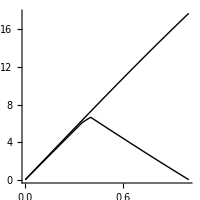

#### BrownNew: dt = 0.05, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO}

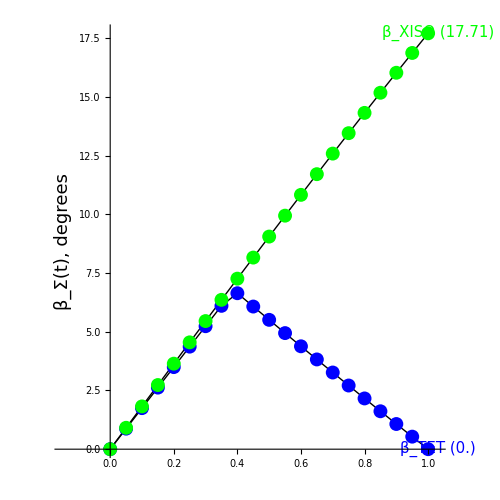

#### BrownTypo: dt = 0.05, Tmat1=TCUBE, Tmat2=TTET, ListSigma = {TET}

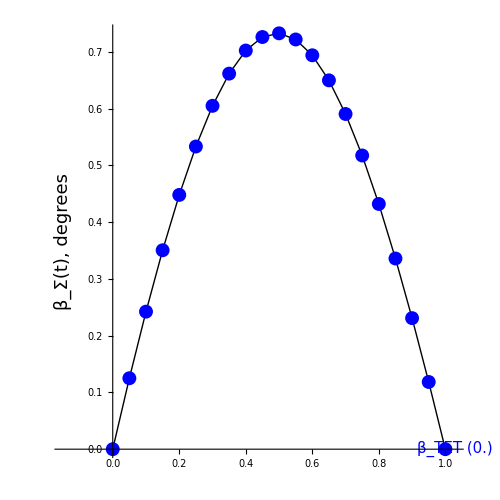

#### BrownTypo: dt = 0.02, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET} (We did not expect to see such a non-differentiable curve.)

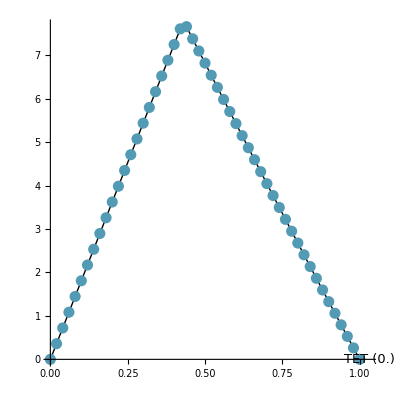

#### BrownTypo: dt = 0.005, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO} t1 = 0.41, t2 = 0.45

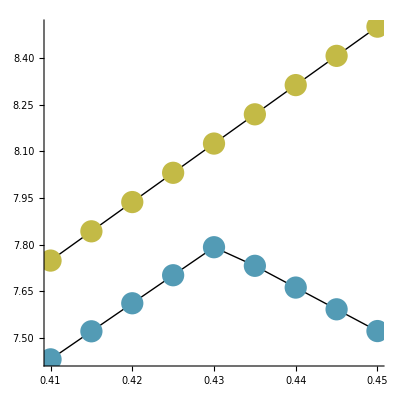

#### BrownTypo: dt = 0.005, Tmat1=closest(TTET,XISO), Tmat2=TTET, ListSigma = {TET,XISO} t1 = 0.38, t2 = 0.40

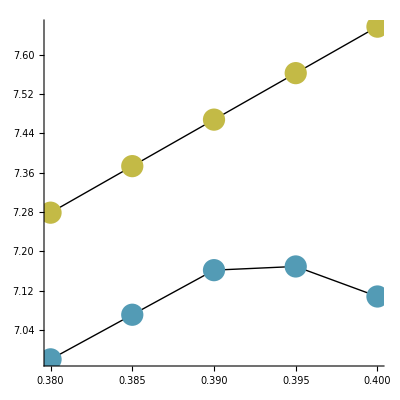

#### Igel: dt = 0.1, ListSigma = all

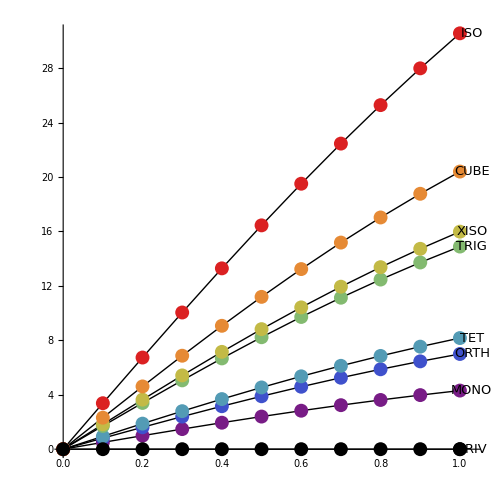

#### Mar17: dt = 0.1, ListSigma = all

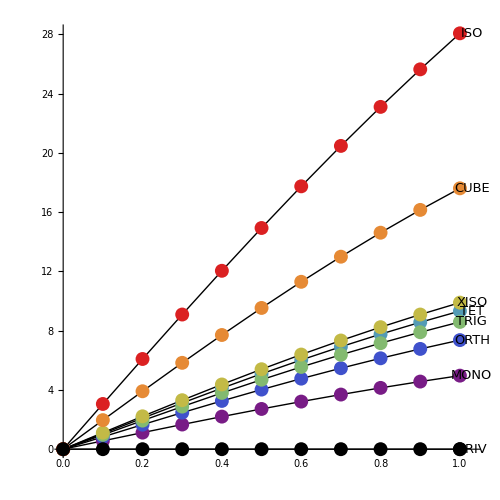

#### BrownTypo: dt = 0.1, ListSigma = all

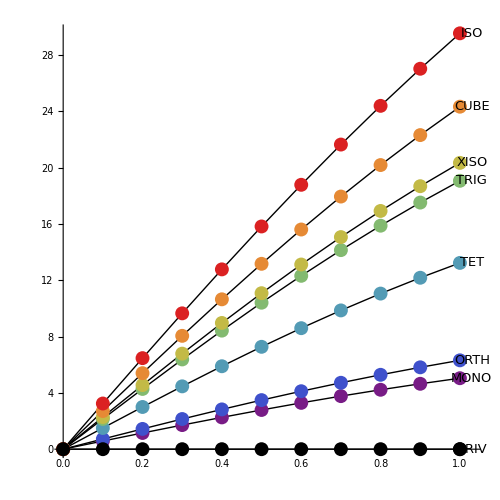

#### BrownNew: tmax = 1.65, dt = 0.05, ListSigma = all